# In-Class Demo (01-13-2022)

## Solving Differential Equations with various initial conditions

Let’s consider the following model for the number of fish living in a pond that is subjected to fishing.  This situation is modeled by the differential equation 
F' = r F(K - F) - q F
where F(t) is the number of fish in the pond at time t, and the parameters r, q, and K are positive constants.  
As part of our analysis, we would like to view the phase line.

First, let’s write the differential equation in the form F' = f(F) where here, we consider r, K, and q as positive constant parameters.  We will also define a function called fPrime that will be used later in the linearization of the ODE.  Here, fPrime is simply given by the following calculation.  First, we simplify the function f(F) to find

f(F) = r F (K - F) - q F
=(r K - q)F - r F^2
so that when we differentiate with respect to F, we find
f'(F) =(r K - q) - 2r F
For simplicity, we will let r = K = 1 for the rest of this Mathematica notebook and demonstration thus reducing the problem to depend only on the parameter q.

```mathematica
f[F_,q_] = F (1 - F) - q F
fPrime[F_,q_]=D[f[F,q],F]
```

(1-F) F-F q

1-2 F-q

Now, let’s find the equilibrium points as a function of the parameter q so that we can visualize them on plots.  We can do this using the Solve command in Mathematica as follows:

```mathematica
eqPts[q_]=Solve[f[F,q]==0,F]
```

{{F→0},{F→1-q}}

Notice that we get a list of equilibrium points.  

Now that we have the equilibrium points, we could plot F' vs F to determine the phase-line.  However, since both f(F,q) and the equilibrium points both depend on the parameter q, we can’t simply graph these without choosing a value of q.  For the first example, let’s choose q=1/2, and let’s consider F to satisfy -2≤F≤2.

Warning: yes, I am considering a negative number of fish (F(t)) in this example.  While not physically realistic, it is illustrative from a mathematical standpoint.

In the code below, we have the following: 
1. p1 is a plot of F' vs F with the value of q = 1/2 substituted in
2. p2 is a ListPlot of the equilibrium points given by the point (F^*,0) where we have used  {F, 0}\.eqPts[1/2] to create a list of points with the equilibrium points substituted in.  
3. The command Show[p1,p2] shows both graphs on the same plot.

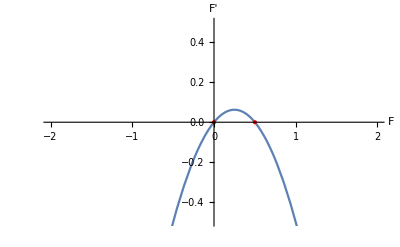

```mathematica
p1 = Plot[f[F,1/2],{F,-2,2}]; 
p2 = ListPlot[{F,0}/.eqPts[1/2],PlotStyle->{Red,PointSize[Large]}]; 
Show[p1,p2, PlotRange->{{-2,2},{-1/2,1/2}},AxesLabel->{F,F'}]
```

Clearly from the above, we can draw the following conclusions:

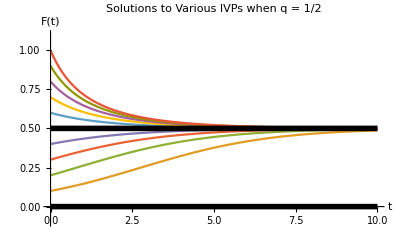

```mathematica
sol[α_,q_] := Quiet[DSolve[{D[F[t],t]==f[F[t],q],F[0] == α},F[t],t]];
p3 = Quiet[Plot[Evaluate[Table[F[t]/.sol[α,1/2],{α,0,1,.1}]],{t,0,10},
PlotRange->{-.1,1.1},
PlotLabel->"Solutions to Various IVPs when q = 1/2",
AxesLabel->{"t","y(t)"}]];
p4 =Plot[F/.eqPts[1/2],{t,0,10},
PlotStyle->{{Black,Thickness[.01]}}] ;
Show[p3,p4,
AxesLabel->{t,F[t]}]
```

Here’s we will do the same thing, but we will also show the equilibrium solutions on the plot as well.  The variable p1 represents the same plot as before, while p2 represents the equilibrium solutions.  The Show command allows us to display both plots on the same graph within the same Manipulate.

```mathematica
Manipulate[
p1 = Plot[f[F,q],{F,-2,2}]; 
p2 = ListPlot[{F,0}/.eqPts[q],PlotStyle->{Black,PointSize[Large]}]; 
P1 = Show[p1,p2, 
PlotRange->{{-2,2},{-1/2,1/2}},
AxesLabel->{F,F'},
PlotLabel->"F' vs F when q = "<>ToString[q],
ImageSize->Large];
p3 = Quiet[Plot[Evaluate[Table[F[t]/.sol[α,q],{α,0,1,.1}]],{t,0,10},PlotRange->{-.1,1.1}]];
p4 =Plot[F/.eqPts[q],{t,0,10},
PlotStyle->{{Black,Thickness[.01]}}] ;
P2 = Show[p3,p4,
AxesLabel->{t,F[t]},
PlotRange->{-.1,1.1},
PlotLabel->"Solutions to Various IVPs when q = "<>ToString[q],
AxesLabel->{"t","y(t)"},
ImageSize->Large];
GraphicsGrid[{{P1,P2}},ImageSize->Full],
{q,Table[j/4.,{j,0,6}]}]
```

## Creating a Bifurcation Plot

Remember, the stability is determined by the value of f'(F) evaluated at each of the equilibrium points.  Here, we will look at each equilibrium point and determine the value of f'(F^*,q).

Note that eqPts[q][[1]] returns the first equilibrium point that the Solve command returned.

```mathematica
Fs1 = eqPts[q][[1]]
Simplify[fPrime[F,q]/.Fs1]
```

{F→0}

1-q

Thus, if q<1, then we see that F'(0) > 0.  Thus, the equilibrium point F_1^* = 0 is unstable when q<1.  Likewise, when q>1, the equilibrium point F_1^* = 0 becomes stable.
Now, let’s look at the other equilibrium point F_2^* = 1-q

```mathematica
Fs2 = eqPts[q][[2]]
Simplify[fPrime[F,q]/.Fs2]
```

{F→1-q}

-1+q

Thus, if q<1, then we see that F'(1-q) < 0.  Thus, the equilibrium point F_2^* =1-q is stable when q<1.  Likewise, when q>1, the equilibrium point F_2^* = 1-q becomes unstable.

It’s worth noting that the two different equilibrium points (F_1^* = 0 and F_2^*=1-q) collide when q = 1.  At this collision, there is a change of stability!  

The following code builds a routine the demonstrates how the equilibrium points change as a function of a parameter.  Thanks to the Winter 2020 Math 3440 for contributing to this code with the help of StackExchange!  You are welcome to use this code to help you throughout the quarter.  Please ask how it works if you have questions!

```mathematica
BifurcationPlot[eqpts_,fPrime_,varrange_,plotCommands_]:=Module[{plotStable,plotUnstable,condition},
For[j=1,j≤Length[eqpts],j++,
condition=Simplify[(fPrime/.eqpts[[j]])]<0;
Subscript[plotStable, j] = Plot[If[condition,Evaluate[eqpts[[j,1,2]]]],varrange,PlotStyle->{Black,Thick}];
Subscript[plotUnstable, j]=Plot[If[Not[condition],Evaluate[eqpts[[j,1,2]]]],varrange,PlotStyle->{Red,Thick,Dashed}]];
Show[Table[{Subscript[plotStable, j],Subscript[plotUnstable, j]},{j,1,Length[eqpts]}],PlotRange->All,plotCommands]]
```

Now that we have defined the “BifurcationPlot” command, we can call it as follows:

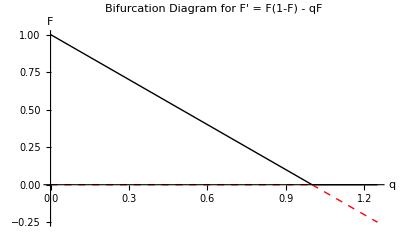

```mathematica
p5 = BifurcationPlot[eqPts[q],fPrime[F,q],{q,0,1.25},
{
PlotLabel->"Bifurcation Diagram for F' = F(1-F) - qF",
AxesLabel->{"q","F"}
}]
```

What the above figure allows us to see is just how the phase line changes as the parameters change.  The following block of code is solely meant for you to be able to visualize what is going on all at the same time.  You don’t need to know how to code the following.  Just simply run it and watch the resulting images.

```mathematica
animateImages=Table[qq,{qq,0,1.25,.125}];
For[j=1,j≤Length[animateImages],j++,
qq=animateImages[[j]];
p5=BifurcationPlot[eqPts[q],fPrime[F,q],{q,0,1.25},
{
PlotLabel->"Bifurcation Diagram for F' = F(1-F) - qF",
AxesLabel->{"q","F"}
}];
p6 = ListPlot[{qq,F}/.eqPts[qq],
PlotStyle->{Black,PointSize[Large]}];
P5=Show[p5,p6,
PlotRange->{-.3,1.25}];
p1 = Plot[f[F,qq],{F,-2,2}]; 
p2 = ListPlot[{F,0}/.eqPts[qq],PlotStyle->{Black,PointSize[Large]}]; 
P1 = Show[p1,p2, 
PlotRange->{{-2,2},{-1/2,1/2}},
AxesLabel->{F,F'},
PlotLabel->"F' vs F when q = "<>ToString[qq]];
p3 = Quiet[Plot[Evaluate[Table[F[t]/.sol[α,qq],{α,-.2,1,.1}]],{t,0,10},PlotRange->{-.1,1.1}]];
p4 =Plot[F/.eqPts[qq],{t,0,10},
PlotStyle->{{Black,Thickness[.01]}}] ;
P2 = Show[p3,p4,
AxesLabel->{t,F[t]},
PlotRange->{-.3,1.25},
PlotLabel->"Solutions to Various IVPs when q = "<>ToString[qq],
AxesLabel->{"t","y(t)"}];
animateImages[[j]]=GraphicsGrid[{{P1,P5,P2}},ImageSize->Full]];
rasterizedFrames=Map[Image,animateImages];
```

```mathematica
ListAnimate[rasterizedFrames,ImageSize->Full]
```